{{Time/Hamming distance,0,1,2,3},{π/4,0.141,0.377,0.361,0.121},{π/2,0,0.0055,0.117,0.877},{3π/4,0.141,0.398,0.36,0.11},{π,0.97,0.03,0.0007,0}}

{{Time/Hamming distance,0,1,2,3},{π/4,0.124,0.378,0.377,0.121},{π/2,0,0,0,1},{3π/4,0.122,0.379,0.374,0.126},{π,1,0,0,0}}

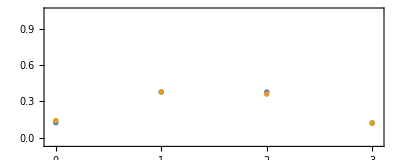

Curve1.png

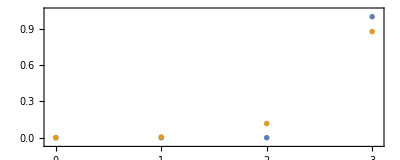

Curve2.png

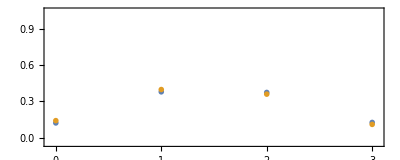

Curve3.png

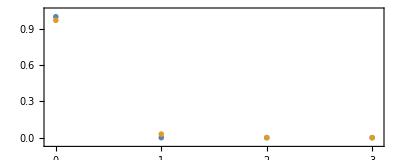

Curve4.png

```mathematica
SetDirectory[NotebookDirectory[]];

ImportDataExp=Import["ind_qubits_n=3_real.csv","CSV"]
xDataExp=Drop[ImportDataExp[[1]],1];
yData1Exp=Drop[ImportDataExp[[2]],1];
yData2Exp=Drop[ImportDataExp[[3]],1];
yData3Exp=Drop[ImportDataExp[[4]],1];
yData4Exp=Drop[ImportDataExp[[5]],1];

ImportDataTheory=Import["ind_qubits_n=3_sim.csv","CSV"]
xDataTheory=Drop[ImportDataTheory[[1]],1];
yData1Theory=Drop[ImportDataTheory[[2]],1];
yData2Theory=Drop[ImportDataTheory[[3]],1];
yData3Theory=Drop[ImportDataTheory[[4]],1];
yData4Theory=Drop[ImportDataTheory[[5]],1];

PlotData1Exp=Table[{xDataExp[[i]],yData1Exp[[i]]},{i,1,Length[xDataExp]}];
PlotData2Exp=Table[{xDataExp[[i]],yData2Exp[[i]]},{i,1,Length[xDataExp]}];
PlotData3Exp=Table[{xDataExp[[i]],yData3Exp[[i]]},{i,1,Length[xDataExp]}];
PlotData4Exp=Table[{xDataExp[[i]],yData4Exp[[i]]},{i,1,Length[xDataExp]}];

PlotData1Theory=Table[{xDataTheory[[i]],yData1Theory[[i]]},{i,1,Length[xDataTheory]}];
PlotData2Theory=Table[{xDataTheory[[i]],yData2Theory[[i]]},{i,1,Length[xDataTheory]}];
PlotData3Theory=Table[{xDataTheory[[i]],yData3Theory[[i]]},{i,1,Length[xDataTheory]}];
PlotData4Theory=Table[{xDataTheory[[i]],yData4Theory[[i]]},{i,1,Length[xDataTheory]}];

PlotRangeX1=0-0.05;
PlotRangeX2=Length[xDataExp]-1+0.05;
PlotRangeY1=0-0.05;
PlotRangeY2=1+0.05;

DataPSize=0.05;
AspRatio=2/5;

ExportPlot=ListPlot[{PlotData1Theory,PlotData1Exp}
(*,Epilog->Text[Style["Θ=π/4",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,None},{{0,1,2,3},None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve1.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve1.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

ExportPlot=ListPlot[{PlotData2Theory,PlotData2Exp}
(*,Epilog->Text[Style["Θ=π/2",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,None},{{0,1,2,3},None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve2.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve2.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

ExportPlot=ListPlot[{PlotData3Theory,PlotData3Exp}
(*,Epilog->Text[Style["Θ=3π/4",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,None},{{0,1,2,3},None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve3.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve3.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

ExportPlot=ListPlot[{PlotData4Theory,PlotData4Exp}
(*,Epilog->Text[Style["Θ=π",FontSize->13],Scaled[{.5,.9}]]*)
,PlotStyle->{PointSize[DataPSize],PointSize[DataPSize]},Joined->False
,PlotStyle->{
{RGBColor["#F3901A"]},
{RGBColor["#7C64A9"]}}
,Frame->True
,FrameTicks->{{All,None},{{0,1,2,3},None}}
,PlotRange->{{PlotRangeX1,PlotRangeX2},{PlotRangeY1,PlotRangeY2}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->15]
,AspectRatio->AspRatio
(*,FrameLabel->{{"Detection probability",None},{"Hamming distance",None}}*)
,PlotMarkers->{"OpenMarkers", Large}
]
Export["Curve4.png",ExportPlot,ImageResolution->300,Background->None]
(*Export["Curve4.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)

Quit[];

(*

chshDataAll=Table[Around[chshData[[i]],chshDataDev[[i]]],{i,1Length[chshData]}];
rewardDataModAll=Table[Around[rewardDataMod[[i]],rewardDataModDev[[i]]],{i,1Length[rewardData]}];

TicksY1={2,2.2,2.4,2.6,2 √2};
TicksY2a={0,0.2,0.4,0.6,0.8,1};(*{{2,0},{2.2,0},{2 √2,1}};*)
TicksY2b=(2 √2-2)TicksY2a+2;
TicksY2=Join[ArrayReshape[TicksY2b,{Length[TicksY2a],1}],ArrayReshape[TicksY2a,{Length[TicksY2a],1}],2];
TicksX={1,10,20,30,40,50};

ExportPlot=ListLinePlot[{rewardDataModAll,AnalyticalBest,chshDataAll}
,PlotStyle->{
{RGBColor["#ff8c00"](*RGBColor["#336688"]*),Thickness[0.005]},
{RGBColor["#3C4D9A"],Thickness[0.005],Dashed},
{RGBColor["#3C4D9A"],Thickness[0.005]}}
,Frame->True
,FrameTicks->{{TicksY1,TicksY2},{TicksX,None}}
,FrameLabel->{{"CHSH value, β","reward, r"},{"trial, t",None}}
,LabelStyle->Directive[Black,FontFamily->"Latin Modern Roman",FontSize->13]
,PlotRange->{{1,LengthTotal},{2-0.05,2*√2+0.05}}
,FrameStyle->{Black,RGBColor["#3C4D9A"],Black,RGBColor["#ff8c00"]}
,AspectRatio->2/5
,IntervalMarkers->"Bands" (*Error Bars*)
]
Export["Curve.png",ExportPlot,ImageResolution->300,Background->None]
Export["Curve.eps",ExportPlot,Background->None,"EmbeddedFonts"->True]*)
Quit[];
```